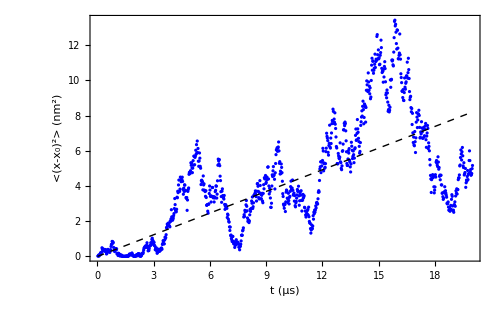

```mathematica
SetDirectory["~/Dropbox/Teaching/Github/PHYS6328-C/3-Langevin_integrators/"];
kT=4.1;
zeta=20;
Dcoeff=kT/zeta;
data=Import["trajectory_brownian.txt","csv"];
dataplot=ListPlot[data,PlotStyle->Blue];
theoryplot=Plot[2 Dcoeff t,{t,0,20},PlotStyle->{Black,Thick,Dashed}];
combinedplot=Show[
dataplot,theoryplot,
PlotRange->All,
Frame->True,Axes->False,FrameStyle->Thick,
FrameLabel->{"t (μs)","<(x-x_0)^2> (nm^2)"},
ImageSize->500,
BaseStyle->{FontSize->20,FontFamily->"Times New Roman"}
];


Show[combinedplot]
Export["plot.eps",combinedplot,"eps"];
```